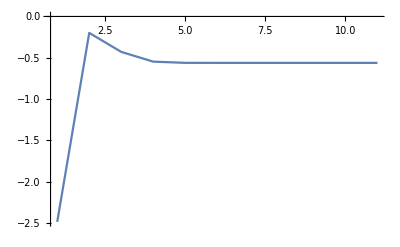

```mathematica
(*Tarea 3*)
(*Daniel Farid Calvo Ramos*)
f[x_]:=x^2-Cos[x]
Ef[x_] =(- D[D[f[x],x],x]/(2*D[f[x],x]));
Ls={0.2,1.7702601243875122,1.033212831100177,0.8433339058427878,0.8243345563998916,0.8241323352972675,0.8241323123025227,0.8241323123025224,0.8241323123025224,0.8241323123025224,0.8241323123025224};
ListLinePlot[Map[Ef, {Ls}], PlotRange->All]
```